## Functions - Define cosine and sine from direction of n_v

Angles using the solutions from 1804.07255

```mathematica
sth[r_,z_,a_,λ_] = a λ r z/(r^2+z^2)^2;
cth[r_,z_,a_,λ_]=1+ a(λ z^2/(r^2+z^2)^2-2);
```

## Some Plots

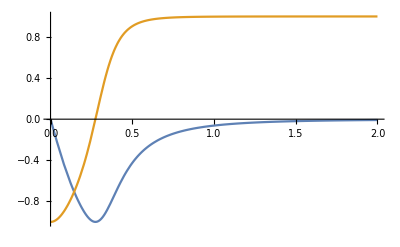

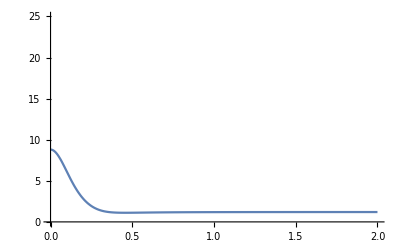

```mathematica
zt=0.2;
at=-0.1;
λt=4;
Plot[{sth[x,zt,at,λt]/Sqrt[cth[x,zt,at,λt]^2+sth[x,zt,at,λt]^2],cth[x,zt,at,λt]/Sqrt[cth[x,zt,at,λt]^2+sth[x,zt,at,λt]^2]},{x,0,2}]
Plot[Sqrt[cth[x,zt,at,λt]^2+sth[x,zt,at,λt]^2],{x,0,2},PlotRange->{0,25}]
```

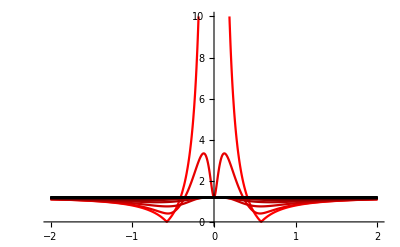

```mathematica
Show[Table[Plot[Sqrt[cth[i,x,at,λt]^2+sth[i,x,at,λt]^2],{x,-2,2},PlotRange->{0,10},PlotStyle->Darker[Red,i/2]],{i,0,3,0.2}]]
```

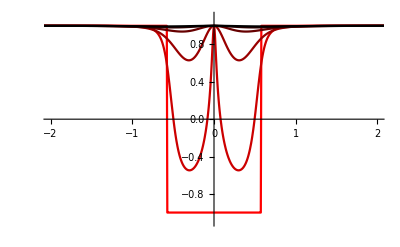

```mathematica
Show[Table[Plot[cth[i,x,at,λt]/Sqrt[cth[i,x,at,λt]^2+sth[i,x,at,λt]^2],{x,-10,10},PlotRange->{{-2,2},{-1.1,1.1}},PlotStyle->Darker[Red,i]],{i,0,1,0.2}]]
```

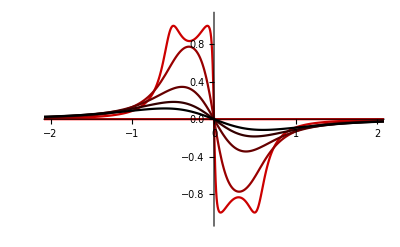

```mathematica
Show[Table[Plot[sth[i,x,at,λt]/Sqrt[cth[i,x,at,λt]^2+sth[i,x,at,λt]^2],{x,-10,10},PlotRange->{{-2,2},{-1.1,1.1}},PlotStyle->Darker[Red,i]],{i,0,1,0.2}]]
```

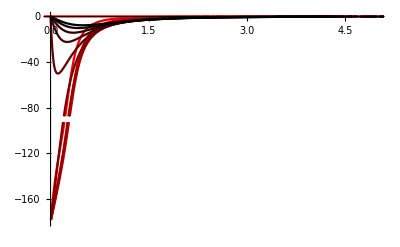

```mathematica
Show[Table[Plot[-ⅈ Log[cth[x,i,at,λt]/Sqrt[cth[x,i,at,λt]^2+sth[x,i,at,λt]^2]+ⅈ sth[x,i,at,λt]/Sqrt[cth[x,i,at,λt]^2+sth[x,i,at,λt]^2]]180/π,{x,-10,10},PlotRange->{{0,5},{-180,0}},PlotStyle->Darker[Red,i]],{i,0,1,0.1}]]
```

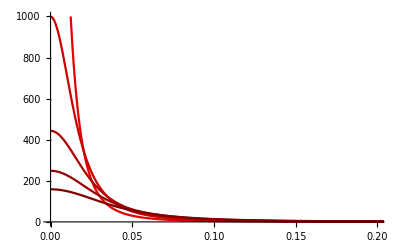

```mathematica
Show[Table[Plot[Sqrt[cth[x,i,at,λt]^2+sth[x,i,at,λt]^2],{x,0,2},PlotRange->{{0,0.2},{0,1000}},PlotStyle->Darker[Red, 10 i]],{i,0.01,0.05,0.01}]]
```

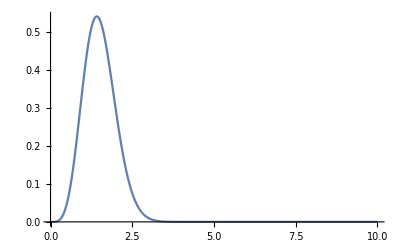

```mathematica
Plot[x^λt Exp[-x^2],{x,0,10},PlotRange->All]
```

## Plots of Vortex Number Density

```mathematica
f[r_,z_,λ_]=λ z^2/(r^2+z^2)^2 - 2;
g[r_,z_,λ_]=λ r z/(r^2+z^2)^2;
```

```mathematica
xt=0.3;
Rpξ = 2;
ωR2 = xt Rpξ^2;
at=(Log[1/xt]+2xt-2)/ωR2
λt=2;
dp=DensityPlot[Log10[Sqrt[cth[x,y,at,λt]^2+sth[x,y,at,λt]^2]],{x,0,Sqrt[λt]/2},{y,-Sqrt[λt]/2,Sqrt[λt]/2},PlotLegends->Automatic,ColorFunctionScaling->False,ColorFunction->ColorData[{"TemperatureMap",{-2,2}}],PlotRange->{{0,0.4 Sqrt[λt]},{-0.4 Sqrt[λt],0.4 Sqrt[λt]},{-1.7,-Log10[xt]}},AspectRatio->2];
disal=ContourPlot[xt Sqrt[(1+at f[r,z,λt])^2+at^2(g[r,z,λt])^2]==1,{r,0,1},{z,-1,1},PlotLegends->Automatic,ContourStyle->{Black,Dashed}];
neg=ContourPlot[y^2/(x^2+y^2)^2==(2-1/at)/λt,{x,0,Sqrt[λt]},{y,-Sqrt[λt],Sqrt[λt]},ContourStyle->{Orange,Dashed}];
cp=ContourPlot[x^2+y^2==0.125λt,{x,0,Sqrt[λt]},{y,-Sqrt[λt],Sqrt[λt]},AspectRatio->{1/2},ContourStyle->{Black,Dashed}];
contdens=ContourPlot[Sqrt[cth[x,y,at,λt]^2+sth[x,y,at,λt]^2],{x,0,Sqrt[λt]/2},{y,-Sqrt[λt]/2,Sqrt[λt]/2},AspectRatio->{1/2},Contours->{0.2,0.5,1.0,1+2Abs[at],1.5,2,1/xt},ColorFunction->"TemperatureMap"];
dist=Rasterize[Show[dp,cp,disal,neg,Frame->True,ImageSize->360,Background->Transparent(*,LabelStyle->{16,FontFamily->"Arial"},FrameLabel->{"ρ/R", "z/R"}*)]]
```

-0.163356

-Graphics-

```mathematica
Sqrt[λt/(2-1/at)]
```

0.496243

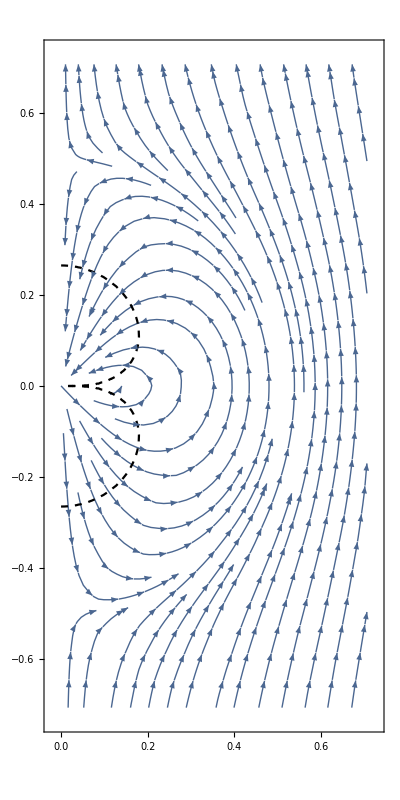

```mathematica
sp=StreamPlot[{ sth[x,y,at,λt]/Sqrt[cth[x,y,at,λt]^2+sth[x,y,at,λt]^2],cth[x,y,at,λt]/Sqrt[cth[x,y,at,λt]^2+sth[x,y,at,λt]^2]},{x,0,Sqrt[λt]/2},{y,-Sqrt[λt]/2,Sqrt[λt]/2},AspectRatio->2];
Show[sp,disal]
```